6.1 Make a list in which the number 1000 is repeated 5 times.

```mathematica
Table[1000, 5]
```

{1000,1000,1000,1000,1000}

6.2 Make a table of the values of n^3 for n from 10 to 20.

```mathematica
Table[n^3, {n, 10, 20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

6.3 Make a number line plot of the first 20 squares.

```mathematica
NumberLinePlot[Table[n^20, {n, 20}]]
```

-Graphics-

6.4 Make a list of the even numbers (2, 4, 6, ...) up to 20.

```mathematica
Range[2, 20, 2]
```

{2,4,6,8,10,12,14,16,18,20}

6.5 Use Table to get the same result as Range[10].

```mathematica
Table[n, {n, 10}]
```

{1,2,3,4,5,6,7,8,9,10}

6.6 Make a bar chart of the first 10 squares.

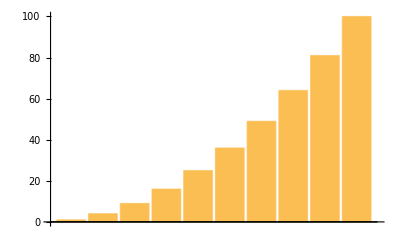

```mathematica
BarChart[Table[n^2, {n, 10}]]
```

6.7 Make a table of lists of digits for the first 10 squares.

```mathematica
Table[IntegerDigits[n^2], {n, 10}]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

6.8 Make a list line plot of the number of digits in each of the first 100 squares.

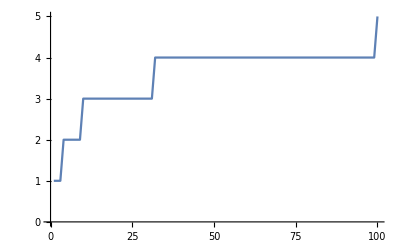

```mathematica
ListLinePlot[Table[Length[IntegerDigits[n^2]], {n, 100}]]
```

6.9 Make a table of the first digits of the first 20 squares.

```mathematica
Table[First[IntegerDigits[n^2]], {n, 20}]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

6.10 Make a list line plot of the first digits of the first 100 squares.

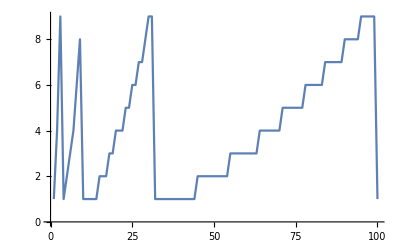

```mathematica
ListLinePlot[Table[First[IntegerDigits[n^2]], {n, 100}]]
```